# Multiscaling analysis of the BVAM model with η =1

## d is the bifurcation parameter

```mathematica
$Assumptions={h∈Reals,a∈Reals,b∈Reals,c∈Reals };
```

```mathematica
pars = {η -> 1};
parsPRE={h->-1,a-> 3/2, b->-0.95, c->1};
```

```mathematica
F= η (U + a V - c U V - U V^2) /. pars ;
G= η (b V + h U + c U V + U V^2) /. pars ;
```

```mathematica
Jcb=({{D[F, U], D[F, V]}, {D[G, U], D[G, V]}})
```

{{1-c V-V^2,a-c U-2 U V},{h+c V+V^2,b+c U+2 U V}}

```mathematica
eqpts=Solve[{F==0, G==0},{U,V}]
```

{{U→0,V→0},{U→((a^2 c)/(2 (a+b))+(a b c)/(a+b)+(b^2 c)/(2 (a+b))+(a √(4 b+a c^2+b c^2-4 a h))/(2 √(a+b))+(b √(4 b+a c^2+b c^2-4 a h))/(2 √(a+b)))/(1+h),V→(-a c-b c-√(a+b) √(4 b+a c^2+b c^2-4 a h))/(2 (a+b))},{U→((a^2 c)/(2 (a+b))+(a b c)/(a+b)+(b^2 c)/(2 (a+b))-(a √(4 b+a c^2+b c^2-4 a h))/(2 √(a+b))-(b √(4 b+a c^2+b c^2-4 a h))/(2 √(a+b)))/(1+h),V→(-a c-b c+√(a+b) √(4 b+a c^2+b c^2-4 a h))/(2 (a+b))}}

```mathematica
J0 = Jcb /. eqpts[[1]];
{{fu,fv},{gu,gv}} = J0;
MatrixForm[J0]
```

(1 | a
h | b)

The dispersion relation:

```mathematica
Λ = λ IdentityMatrix[2] - J0 + k^2 {{d,0},{0,1}};
reldisp = Det[Λ]
```

b-a h-k^2-b d k^2+d k^4-λ-b λ+k^2 λ+d k^2 λ+λ^2

## Weakly nonlinear analysis

Linear term

```mathematica
L={{d,0},{0,1}}.{D[u[x], x,x], D[v[x], x,x]} + Jcb.{u[x],v[x]} /. {U -> u0, V -> v0}
```

{(1-c v0-v0^2) u[x]+(a-c u0-2 u0 v0) v[x]+d u''[x],(h+c v0+v0^2) u[x]+(b+c u0+2 u0 v0) v[x]+v''[x]}

Quadratic term

```mathematica
Q = {{1/2 u[x]^2  D[F, U,U] +  u[x] v[x]  D[F, U,V] + 1/2 v[x]^2  D[F, V,V]}, {1/2 u[x]^2  D[G, U,U] +  u[x] v[x]  D[G, U,V] + 1/2 v[x]^2  D[G, V,V]}} /. {U -> u0, V -> v0}
```

{{(-c-2 v0) u[x] v[x]-u0 v[x]^2},{(c+2 v0) u[x] v[x]+u0 v[x]^2}}

Cubic term

```mathematica
Cu = {{1/6 u[x]^3  D[F, U,U,U] +  1/2 u[x]^2 v[x]  D[F, U,U,V]+1/2 u[x] v[x]^2  D[F, U,V,V] + 1/6 v[x]^3  D[F, V,V,V]}, {1/6 u[x]^3  D[G, U,U,U] +  1/2 u[x]^2 v[x]  D[G, U,U,V]+1/2 u[x] v[x]^2  D[G, U,V,V] + 1/6 v[x]^3  D[G, V,V,V]}} /. {U -> u0, V -> v0}
```

{{-u[x] v[x]^2},{u[x] v[x]^2}}

Consider  the (0,0) equilibrium point:

```mathematica
{u0,v0}={U,V}/.eqpts[[1]];
```

```mathematica
L // MatrixForm
```

(u[x]+a v[x]+d u''[x]
h u[x]+b v[x]+v''[x])

```mathematica
Q // MatrixForm
```

(-c u[x] v[x]
c u[x] v[x])

```mathematica
Cu // MatrixForm
```

(-u[x] v[x]^2
u[x] v[x]^2)

## Multiscale expansion

u[x]= ϵ u1[x] + ϵ^2 u2[x] + ϵ^3 u3[x];
v[x] = ϵ v1[x] + ϵ^2 v2[x] + ϵ^3 v3[x];

```mathematica
uexp =u-> (ϵ u1[#] + ϵ^2 u2[#] + ϵ^3 u3[#]&);
vexp = v-> (ϵ v1[#] + ϵ^2 v2[#] + ϵ^3 v3[#]&);
```

General expression up to cubic order

```mathematica
L /. uexp /. vexp // Expand // MatrixForm
```

(ϵ u1[x]+ϵ^2 u2[x]+ϵ^3 u3[x]+a ϵ v1[x]+a ϵ^2 v2[x]+a ϵ^3 v3[x]+d ϵ u1''[x]+d ϵ^2 u2''[x]+d ϵ^3 u3''[x]
h ϵ u1[x]+h ϵ^2 u2[x]+h ϵ^3 u3[x]+b ϵ v1[x]+b ϵ^2 v2[x]+b ϵ^3 v3[x]+ϵ v1''[x]+ϵ^2 v2''[x]+ϵ^3 v3''[x])

```mathematica
Q /. uexp /. vexp //Expand // MatrixForm
```

(-c ϵ^2 u1[x] v1[x]-c ϵ^3 u2[x] v1[x]-c ϵ^4 u3[x] v1[x]-c ϵ^3 u1[x] v2[x]-c ϵ^4 u2[x] v2[x]-c ϵ^5 u3[x] v2[x]-c ϵ^4 u1[x] v3[x]-c ϵ^5 u2[x] v3[x]-c ϵ^6 u3[x] v3[x]
c ϵ^2 u1[x] v1[x]+c ϵ^3 u2[x] v1[x]+c ϵ^4 u3[x] v1[x]+c ϵ^3 u1[x] v2[x]+c ϵ^4 u2[x] v2[x]+c ϵ^5 u3[x] v2[x]+c ϵ^4 u1[x] v3[x]+c ϵ^5 u2[x] v3[x]+c ϵ^6 u3[x] v3[x])

```mathematica
Cu /. uexp /. vexp //Expand // MatrixForm
```

(-ϵ^3 u1[x] v1[x]^2-ϵ^4 u2[x] v1[x]^2-ϵ^5 u3[x] v1[x]^2-2 ϵ^4 u1[x] v1[x] v2[x]-2 ϵ^5 u2[x] v1[x] v2[x]-2 ϵ^6 u3[x] v1[x] v2[x]-ϵ^5 u1[x] v2[x]^2-ϵ^6 u2[x] v2[x]^2-ϵ^7 u3[x] v2[x]^2-2 ϵ^5 u1[x] v1[x] v3[x]-2 ϵ^6 u2[x] v1[x] v3[x]-2 ϵ^7 u3[x] v1[x] v3[x]-2 ϵ^6 u1[x] v2[x] v3[x]-2 ϵ^7 u2[x] v2[x] v3[x]-2 ϵ^8 u3[x] v2[x] v3[x]-ϵ^7 u1[x] v3[x]^2-ϵ^8 u2[x] v3[x]^2-ϵ^9 u3[x] v3[x]^2
ϵ^3 u1[x] v1[x]^2+ϵ^4 u2[x] v1[x]^2+ϵ^5 u3[x] v1[x]^2+2 ϵ^4 u1[x] v1[x] v2[x]+2 ϵ^5 u2[x] v1[x] v2[x]+2 ϵ^6 u3[x] v1[x] v2[x]+ϵ^5 u1[x] v2[x]^2+ϵ^6 u2[x] v2[x]^2+ϵ^7 u3[x] v2[x]^2+2 ϵ^5 u1[x] v1[x] v3[x]+2 ϵ^6 u2[x] v1[x] v3[x]+2 ϵ^7 u3[x] v1[x] v3[x]+2 ϵ^6 u1[x] v2[x] v3[x]+2 ϵ^7 u2[x] v2[x] v3[x]+2 ϵ^8 u3[x] v2[x] v3[x]+ϵ^7 u1[x] v3[x]^2+ϵ^8 u2[x] v3[x]^2+ϵ^9 u3[x] v3[x]^2)

Then  this  is the right hand side of the perturbed RD equation

```mathematica
rhs=Expand[(L + Q + Cu) /. uexp /. vexp]
```

{{ϵ u1[x]+ϵ^2 u2[x]+ϵ^3 u3[x]+a ϵ v1[x]-c ϵ^2 u1[x] v1[x]-c ϵ^3 u2[x] v1[x]-c ϵ^4 u3[x] v1[x]-ϵ^3 u1[x] v1[x]^2-ϵ^4 u2[x] v1[x]^2-ϵ^5 u3[x] v1[x]^2+a ϵ^2 v2[x]-c ϵ^3 u1[x] v2[x]-c ϵ^4 u2[x] v2[x]-c ϵ^5 u3[x] v2[x]-2 ϵ^4 u1[x] v1[x] v2[x]-2 ϵ^5 u2[x] v1[x] v2[x]-2 ϵ^6 u3[x] v1[x] v2[x]-ϵ^5 u1[x] v2[x]^2-ϵ^6 u2[x] v2[x]^2-ϵ^7 u3[x] v2[x]^2+a ϵ^3 v3[x]-c ϵ^4 u1[x] v3[x]-c ϵ^5 u2[x] v3[x]-c ϵ^6 u3[x] v3[x]-2 ϵ^5 u1[x] v1[x] v3[x]-2 ϵ^6 u2[x] v1[x] v3[x]-2 ϵ^7 u3[x] v1[x] v3[x]-2 ϵ^6 u1[x] v2[x] v3[x]-2 ϵ^7 u2[x] v2[x] v3[x]-2 ϵ^8 u3[x] v2[x] v3[x]-ϵ^7 u1[x] v3[x]^2-ϵ^8 u2[x] v3[x]^2-ϵ^9 u3[x] v3[x]^2+d ϵ u1''[x]+d ϵ^2 u2''[x]+d ϵ^3 u3''[x]},{h ϵ u1[x]+h ϵ^2 u2[x]+h ϵ^3 u3[x]+b ϵ v1[x]+c ϵ^2 u1[x] v1[x]+c ϵ^3 u2[x] v1[x]+c ϵ^4 u3[x] v1[x]+ϵ^3 u1[x] v1[x]^2+ϵ^4 u2[x] v1[x]^2+ϵ^5 u3[x] v1[x]^2+b ϵ^2 v2[x]+c ϵ^3 u1[x] v2[x]+c ϵ^4 u2[x] v2[x]+c ϵ^5 u3[x] v2[x]+2 ϵ^4 u1[x] v1[x] v2[x]+2 ϵ^5 u2[x] v1[x] v2[x]+2 ϵ^6 u3[x] v1[x] v2[x]+ϵ^5 u1[x] v2[x]^2+ϵ^6 u2[x] v2[x]^2+ϵ^7 u3[x] v2[x]^2+b ϵ^3 v3[x]+c ϵ^4 u1[x] v3[x]+c ϵ^5 u2[x] v3[x]+c ϵ^6 u3[x] v3[x]+2 ϵ^5 u1[x] v1[x] v3[x]+2 ϵ^6 u2[x] v1[x] v3[x]+2 ϵ^7 u3[x] v1[x] v3[x]+2 ϵ^6 u1[x] v2[x] v3[x]+2 ϵ^7 u2[x] v2[x] v3[x]+2 ϵ^8 u3[x] v2[x] v3[x]+ϵ^7 u1[x] v3[x]^2+ϵ^8 u2[x] v3[x]^2+ϵ^9 u3[x] v3[x]^2+ϵ v1''[x]+ϵ^2 v2''[x]+ϵ^3 v3''[x]}}

Let d be the critical parameter.

If the instability arises when d<d_c therefore d-d_c<0 and we propose:

d-d_c=-ϵ d_1-ϵ^2 d_2-ϵ^3 d_3-O(ϵ^4)       ⟹      d=d_c-ϵ d_1-ϵ^2 d_2-ϵ^3 d_3-O(ϵ^4)

```mathematica
expa = d-> dc-ϵ d1-ϵ^2 d2 -ϵ^3 d3;
```

```mathematica
rhs = rhs /. expa // Expand
```

{{ϵ u1[x]+ϵ^2 u2[x]+ϵ^3 u3[x]+a ϵ v1[x]-c ϵ^2 u1[x] v1[x]-c ϵ^3 u2[x] v1[x]-c ϵ^4 u3[x] v1[x]-ϵ^3 u1[x] v1[x]^2-ϵ^4 u2[x] v1[x]^2-ϵ^5 u3[x] v1[x]^2+a ϵ^2 v2[x]-c ϵ^3 u1[x] v2[x]-c ϵ^4 u2[x] v2[x]-c ϵ^5 u3[x] v2[x]-2 ϵ^4 u1[x] v1[x] v2[x]-2 ϵ^5 u2[x] v1[x] v2[x]-2 ϵ^6 u3[x] v1[x] v2[x]-ϵ^5 u1[x] v2[x]^2-ϵ^6 u2[x] v2[x]^2-ϵ^7 u3[x] v2[x]^2+a ϵ^3 v3[x]-c ϵ^4 u1[x] v3[x]-c ϵ^5 u2[x] v3[x]-c ϵ^6 u3[x] v3[x]-2 ϵ^5 u1[x] v1[x] v3[x]-2 ϵ^6 u2[x] v1[x] v3[x]-2 ϵ^7 u3[x] v1[x] v3[x]-2 ϵ^6 u1[x] v2[x] v3[x]-2 ϵ^7 u2[x] v2[x] v3[x]-2 ϵ^8 u3[x] v2[x] v3[x]-ϵ^7 u1[x] v3[x]^2-ϵ^8 u2[x] v3[x]^2-ϵ^9 u3[x] v3[x]^2+dc ϵ u1''[x]-d1 ϵ^2 u1''[x]-d2 ϵ^3 u1''[x]-d3 ϵ^4 u1''[x]+dc ϵ^2 u2''[x]-d1 ϵ^3 u2''[x]-d2 ϵ^4 u2''[x]-d3 ϵ^5 u2''[x]+dc ϵ^3 u3''[x]-d1 ϵ^4 u3''[x]-d2 ϵ^5 u3''[x]-d3 ϵ^6 u3''[x]},{h ϵ u1[x]+h ϵ^2 u2[x]+h ϵ^3 u3[x]+b ϵ v1[x]+c ϵ^2 u1[x] v1[x]+c ϵ^3 u2[x] v1[x]+c ϵ^4 u3[x] v1[x]+ϵ^3 u1[x] v1[x]^2+ϵ^4 u2[x] v1[x]^2+ϵ^5 u3[x] v1[x]^2+b ϵ^2 v2[x]+c ϵ^3 u1[x] v2[x]+c ϵ^4 u2[x] v2[x]+c ϵ^5 u3[x] v2[x]+2 ϵ^4 u1[x] v1[x] v2[x]+2 ϵ^5 u2[x] v1[x] v2[x]+2 ϵ^6 u3[x] v1[x] v2[x]+ϵ^5 u1[x] v2[x]^2+ϵ^6 u2[x] v2[x]^2+ϵ^7 u3[x] v2[x]^2+b ϵ^3 v3[x]+c ϵ^4 u1[x] v3[x]+c ϵ^5 u2[x] v3[x]+c ϵ^6 u3[x] v3[x]+2 ϵ^5 u1[x] v1[x] v3[x]+2 ϵ^6 u2[x] v1[x] v3[x]+2 ϵ^7 u3[x] v1[x] v3[x]+2 ϵ^6 u1[x] v2[x] v3[x]+2 ϵ^7 u2[x] v2[x] v3[x]+2 ϵ^8 u3[x] v2[x] v3[x]+ϵ^7 u1[x] v3[x]^2+ϵ^8 u2[x] v3[x]^2+ϵ^9 u3[x] v3[x]^2+ϵ v1''[x]+ϵ^2 v2''[x]+ϵ^3 v3''[x]}}

Collecting terms

```mathematica
rhs =Collect[rhs,ϵ];
```

```mathematica
Oe1 = Coefficient[rhs,ϵ]
Oe2 = Coefficient[rhs,ϵ,2]
Oe3 = Coefficient[rhs,ϵ,3]
```

{{u1[x]+a v1[x]+dc u1''[x]},{h u1[x]+b v1[x]+v1''[x]}}

{{u2[x]-c u1[x] v1[x]+a v2[x]-d1 u1''[x]+dc u2''[x]},{h u2[x]+c u1[x] v1[x]+b v2[x]+v2''[x]}}

{{u3[x]-c u2[x] v1[x]-u1[x] v1[x]^2-c u1[x] v2[x]+a v3[x]-d2 u1''[x]-d1 u2''[x]+dc u3''[x]},{h u3[x]+c u2[x] v1[x]+u1[x] v1[x]^2+c u1[x] v2[x]+b v3[x]+v3''[x]}}

```mathematica
MatrixForm[Oe1]
MatrixForm[Oe2]
MatrixForm[Oe3]
```

(u1[x]+a v1[x]+dc u1''[x]
h u1[x]+b v1[x]+v1''[x])

(u2[x]-c u1[x] v1[x]+a v2[x]-d1 u1''[x]+dc u2''[x]
h u2[x]+c u1[x] v1[x]+b v2[x]+v2''[x])

(u3[x]-c u2[x] v1[x]-u1[x] v1[x]^2-c u1[x] v2[x]+a v3[x]-d2 u1''[x]-d1 u2''[x]+dc u3''[x]
h u3[x]+c u2[x] v1[x]+u1[x] v1[x]^2+c u1[x] v2[x]+b v3[x]+v3''[x])

Now, for the left hand side,  we scale time as ∂/(∂t)=∂/(∂T_0)+ϵ∂/(∂T_1)+ϵ^2∂/(∂T_2)+ϵ^3∂/(∂T_3)+O(ϵ^4):

```mathematica
lhs = {D[u[x,T0,T1,T2,T3], T0]+ ϵ D[u[x,T0,T1,T2,T3], T1]+ ϵ^2 D[u[x,T0,T1,T2,T3], T2]+ϵ^3 D[u[x,T0,T1,T2,T3], T3]}
```

{ϵ^3 u^(0,0,0,0,1)[x,T0,T1,T2,T3]+ϵ^2 u^(0,0,0,1,0)[x,T0,T1,T2,T3]+ϵ u^(0,0,1,0,0)[x,T0,T1,T2,T3]+u^(0,1,0,0,0)[x,T0,T1,T2,T3]}

```mathematica
expt=u ->( ϵ Subscript[u, 1][#1,#2,#3,#4,#5]+ϵ^2 Subscript[u, 2][#1,#2,#3,#4,#5]+ϵ^3 Subscript[u, 3][#1,#2,#3,#4,#5]&)
```

u→(ϵ u_1[#1,#2,#3,#4,#5]+ϵ^2 u_2[#1,#2,#3,#4,#5]+ϵ^3 u_3[#1,#2,#3,#4,#5]&)

```mathematica
lhs = lhs/.expt // Expand
```

{ϵ^4 u_1^(0,0,0,0,1)[x,T0,T1,T2,T3]+ϵ^5 u_2^(0,0,0,0,1)[x,T0,T1,T2,T3]+ϵ^6 u_3^(0,0,0,0,1)[x,T0,T1,T2,T3]+ϵ^3 u_1^(0,0,0,1,0)[x,T0,T1,T2,T3]+ϵ^4 u_2^(0,0,0,1,0)[x,T0,T1,T2,T3]+ϵ^5 u_3^(0,0,0,1,0)[x,T0,T1,T2,T3]+ϵ^2 u_1^(0,0,1,0,0)[x,T0,T1,T2,T3]+ϵ^3 u_2^(0,0,1,0,0)[x,T0,T1,T2,T3]+ϵ^4 u_3^(0,0,1,0,0)[x,T0,T1,T2,T3]+ϵ u_1^(0,1,0,0,0)[x,T0,T1,T2,T3]+ϵ^2 u_2^(0,1,0,0,0)[x,T0,T1,T2,T3]+ϵ^3 u_3^(0,1,0,0,0)[x,T0,T1,T2,T3]}

```mathematica
lhs =Collect[lhs,ϵ]
```

{ϵ^6 u_3^(0,0,0,0,1)[x,T0,T1,T2,T3]+ϵ^5 (u_2^(0,0,0,0,1)[x,T0,T1,T2,T3]+u_3^(0,0,0,1,0)[x,T0,T1,T2,T3])+ϵ^4 (u_1^(0,0,0,0,1)[x,T0,T1,T2,T3]+u_2^(0,0,0,1,0)[x,T0,T1,T2,T3]+u_3^(0,0,1,0,0)[x,T0,T1,T2,T3])+ϵ u_1^(0,1,0,0,0)[x,T0,T1,T2,T3]+ϵ^2 (u_1^(0,0,1,0,0)[x,T0,T1,T2,T3]+u_2^(0,1,0,0,0)[x,T0,T1,T2,T3])+ϵ^3 (u_1^(0,0,0,1,0)[x,T0,T1,T2,T3]+u_2^(0,0,1,0,0)[x,T0,T1,T2,T3]+u_3^(0,1,0,0,0)[x,T0,T1,T2,T3])}

```mathematica
Oe1t = Coefficient[lhs,ϵ]
Oe2t = Coefficient[lhs,ϵ,2]
Oe3t = Coefficient[lhs,ϵ,3]
```

{u_1^(0,1,0,0,0)[x,T0,T1,T2,T3]}

{u_1^(0,0,1,0,0)[x,T0,T1,T2,T3]+u_2^(0,1,0,0,0)[x,T0,T1,T2,T3]}

{u_1^(0,0,0,1,0)[x,T0,T1,T2,T3]+u_2^(0,0,1,0,0)[x,T0,T1,T2,T3]+u_3^(0,1,0,0,0)[x,T0,T1,T2,T3]}

### O(ϵ): (u_1, v_1)

The O (ϵ) system is:

 ∂/(∂T_0)(u_1
v_1) = (d_c | 0
0 | 1)(u_1
v_1)''+ (1 | a
h | b)(u_1
v_1)

which is the linearized BVAM model. Since at criticality λ-> 0 then the solution is time independent and, in general (∂u)/(∂T_0)=0. 
We propose the ansatz

(u_1
v_1) = (U_1
V_1)A(t) Cos[k x]

```mathematica
Oe1 // MatrixForm
```

(u1[x]+a v1[x]+dc u1''[x]
h u1[x]+b v1[x]+v1''[x])

```mathematica
u1[x] = U1 A[t] Cos[k x];
v1[x] = V1 A[t] Cos[k x];
u1''[x] = D[u1[x],{x,2}]
v1''[x] = D[v1[x],{x,2}]
```

-k^2 U1 A[t] Cos[k x]

-k^2 V1 A[t] Cos[k x]

```mathematica
Oe1 = FullSimplify[Oe1]
```

{{(U1-dc k^2 U1+a V1) A[t] Cos[k x]},{(h U1+(b-k^2) V1) A[t] Cos[k x]}}

```mathematica
MatrixForm[Oe1]
```

((U1-dc k^2 U1+a V1) A[t] Cos[k x]
(h U1+(b-k^2) V1) A[t] Cos[k x])

```mathematica
Coefficient[Oe1,U1] // MatrixForm
Coefficient[Oe1,V1] // MatrixForm
```

((1-dc k^2) A[t] Cos[k x]
h A[t] Cos[k x])

(a A[t] Cos[k x]
(b-k^2) A[t] Cos[k x])

```mathematica
M=Join[Coefficient[Oe1,U1],Coefficient[Oe1,V1],2]
```

{{(1-dc k^2) A[t] Cos[k x],a A[t] Cos[k x]},{h A[t] Cos[k x],(b-k^2) A[t] Cos[k x]}}

```mathematica
MatrixForm[M] // FullSimplify
```

((1-dc k^2) A[t] Cos[k x] | a A[t] Cos[k x]
h A[t] Cos[k x] | (b-k^2) A[t] Cos[k x])

We  notice  that  A(t) Cos[kx] is a common factor, then

```mathematica
M=M /. {x->0, A[t]->1}
```

{{1-dc k^2,a},{h,b-k^2}}

```mathematica
MatrixForm[M]
```

(1-dc k^2 | a
h | b-k^2)

Critical value of a

```mathematica
β=Det[M]
```

b-a h-k^2-b dc k^2+dc k^4

```mathematica
dckc=Solve[{β==0, D[β,k]==0},{dc,k}]
```

{{dc→(b-2 a h+2 √(-a h (b-a h)))/b^2,k→-√(b-a h-√(-a h (b-a h)))},{dc→(b-2 a h+2 √(-a h (b-a h)))/b^2,k→√(b-a h-√(-a h (b-a h)))},{dc→(b-2 a h-2 √(-a h (b-a h)))/b^2,k→-√(b-a h+√(-a h (b-a h)))},{dc→(b-2 a h-2 √(-a h (b-a h)))/b^2,k→√(b-a h+√(-a h (b-a h)))}}

```mathematica
dckc /. pars/.parsPRE
```

{{dc→4.28431,k→0.-0.598578 ⅈ},{dc→4.28431,k→0.+0.598578 ⅈ},{dc→0.258626,k→-1.2076},{dc→0.258626,k→1.2076}}

```mathematica
{dc,kc} ={dc,k} /. dckc[[4]] // FullSimplify
```

{1/(b-2 a h+2 √(a h (-b+a h))),√(b-a h+√(a h (-b+a h)))}

```mathematica
{lm,lp} = λ /. Solve[reldisp==0,λ]
```

{1/2 (1+b-k^2-d k^2-√((-1-b+k^2+d k^2)^2-4 (b-a h-k^2-b d k^2+d k^4))),1/2 (1+b-k^2-d k^2+√((-1-b+k^2+d k^2)^2-4 (b-a h-k^2-b d k^2+d k^4)))}

```mathematica
eles = {lm,lp}/. d->dc/.pars/.parsPRE
```

{1/2 (0.05-1.25863 k^2-√((-0.05+1.25863 k^2)^2-4 (0.55-0.754305 k^2+0.258626 k^4))),1/2 (0.05-1.25863 k^2+√((-0.05+1.25863 k^2)^2-4 (0.55-0.754305 k^2+0.258626 k^4)))}

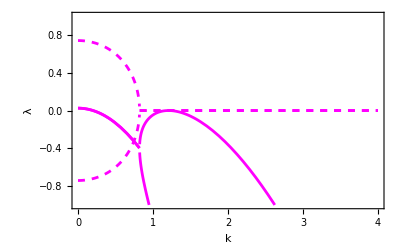

```mathematica
Plot[{Im[eles],Re[eles] },{k,0,4},PlotRange-> {-1,1},PlotStyle-> {{Dashed,Magenta},{Magenta}}, Frame-> True,FrameLabel -> {k,λ}]
```

```mathematica
eles = {lm,lp}/.d->dc-0.1 /.pars/.parsPRE
```

{1/2 (0.05-1.15863 k^2-√((-0.05+1.15863 k^2)^2-4 (0.55-0.849305 k^2+0.158626 k^4))),1/2 (0.05-1.15863 k^2+√((-0.05+1.15863 k^2)^2-4 (0.55-0.849305 k^2+0.158626 k^4)))}

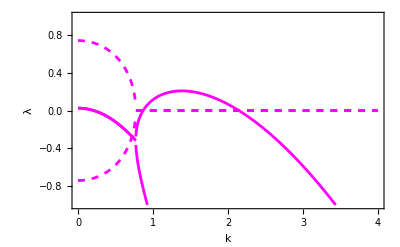

```mathematica
Plot[{Im[eles],Re[eles] },{k,0,4},PlotRange-> {-1,1},PlotStyle-> {{Dashed,Magenta},{Magenta}}, Frame-> True,FrameLabel -> {k,λ}]
```

```mathematica
eles = {lm,lp}/.d->dc+0.1 /.pars/.parsPRE
```

{1/2 (0.05-1.35863 k^2-√((-0.05+1.35863 k^2)^2-4 (0.55-0.659305 k^2+0.358626 k^4))),1/2 (0.05-1.35863 k^2+√((-0.05+1.35863 k^2)^2-4 (0.55-0.659305 k^2+0.358626 k^4)))}

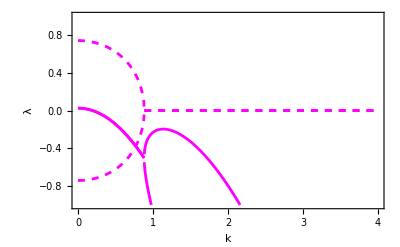

```mathematica
Plot[{Im[eles],Re[eles] },{k,0,4},PlotRange-> {-1,1},PlotStyle-> {{Dashed,Magenta},{Magenta}}, Frame-> True,FrameLabel -> {k,λ}]
```

```mathematica
Oe1
```

{{(U1-(k^2 U1)/(b-2 a h+2 √(a h (-b+a h)))+a V1) A[t] Cos[k x]},{(h U1+(b-k^2) V1) A[t] Cos[k x]}}

```mathematica
M =FullSimplify[M/. k-> kc]
```

{{(a h+√(a h (-b+a h)))/b,a},{h,a h-√(a h (-b+a h))}}

```mathematica
MatrixForm[M]
```

((a h+√(a h (-b+a h)))/b | a
h | a h-√(a h (-b+a h)))

The usual election of eigenvectors of a matrix M with a unique real critical eigenvector (i.e. Det[M]=0 and Tr[m]≠0), is
(1
-M_11/M_12)
(see Nicolis, Eq. 5.14). Then

```mathematica
{U1,V1} =FullSimplify[{1,-M[[1,1]]/M[[1,2]]}, Assumptions->{b<0 &&a<0}]
```

{1,1/(-a+(√(a h (-b+a h)))/h)}

Thus, (u1, v1) is given by

(u_1
v_1) = (1
1/((√(a h (-b+a h)))/h-a))A Cos[k_c x].

For the next steps we assume that A=A(T_1, T_2), thus

```mathematica
u1[x] = U1 A[t] Cos[k x];
v1[x] = V1 A[t] Cos[k x];
u1''[x] = D[u1[x],{x,2}];
v1''[x] = D[v1[x],{x,2}];
```

### O(ϵ^2): (u_2, v_2)

From this, the O(ϵ^2) system is

∂/(∂t_0)(u_2
v_2) + ∂/(∂t_1)(u_1
v_1)=(d_c | 0
0 | 1)(u_2
v_2)''+  (1 | a
h | b)(u_2
v_2)+ (-c u_1 v_1-d_1 u''_1 
c u_1 v_1)
or
(d_c | 0
0 | 1)(u_2
v_2)''+ (1 | a
h | b)(u_2
v_2)-∂/(∂t_0)(u_2
v_2)= q_2
where
q_2=∂/(∂T_1)(u_1
v_1)-(-c u_1 v_1-d_1 u''_1 
c u_1 v_1)
depends only on the previous solution (u_1, v_1).

Since ∂/(∂t_0)=0, the O(ϵ^2) system can be written as
ℒ(u_2
v_2)=q_2
The solvability condition requires that
⟨(u_2^†
v_2^†), q_2⟩=0,
where (u_2^†
v_2^†) is the nullvector of ℒ^†, i.e., 
ℒ^†(u_2^†
v_2^†)=(0
0).

```mathematica
q2 = ({{D[u1[x], t]}, {D[v1[x], t]}}) -(Oe2 /. {u2[x]->0, v2[x]->0,u2''[x]->0,v2''[x]->0})
```

{{-d1 k^2 A[t] Cos[k x]+(c A[t]^2 Cos[k x]^2)/(-a+(√(a h (-b+a h)))/h)+Cos[k x] A'[t]},{-(c A[t]^2 Cos[k x]^2)/(-a+(√(a h (-b+a h)))/h)+(Cos[k x] A'[t])/(-a+(√(a h (-b+a h)))/h)}}

```mathematica
MatrixForm[q2]
```

(-d1 k^2 A[t] Cos[k x]+(c A[t]^2 Cos[k x]^2)/(-a+(√(a h (-b+a h)))/h)+Cos[k x] A'[t]
-(c A[t]^2 Cos[k x]^2)/(-a+(√(a h (-b+a h)))/h)+(Cos[k x] A'[t])/(-a+(√(a h (-b+a h)))/h))

The Fredholm alternative
Let us consider that Ω=(0,l); the eigenfuntions of the Newman problem are Cos[(n π)/l x], where k=(n π)/l are the wavenumbers, then l=(n π)/k.
The solvability condition requires
⟨u^†, q_2⟩ = 0
In this case:
⟨u^†, q_2⟩ = ∫_0^l (u^†)^T q_2 ⅆx =∫_0^((n π)/k) (u^†)^T q_2 ⅆx

```mathematica
L2IP[z_:List, y_:List, Assum_:List] := Flatten[Integrate[Transpose[z].y,{x,0,(n π)/k}, Assumptions -> Assum ]]
```

We can easily verify that   (d^2 u)/dx^2 is self-adjoint with both, Dirichlet and Newmann boundary conditions (see SMF notes), then 
ℒ^† = (d_c d^2/dx^2 | 0
0 | d^2/dx^2)+ (1 | a
h | b)^T=(d_c d^2/dx^2 | 0
0 | d^2/dx^2)+ (1 | h
a | b)
Assume
(u_2^†
v_2^†) = (W_1
W_2)Cos[k_c x].

```mathematica
matrix = Flatten[Normal[CoefficientArrays[Oe2 /. {u2''[x]->0,v2''[x]->0, A[t]->0}//Chop,{u2[x],v2[x]}]][[2]],1];
MatrixForm[matrix]
```

(1 | a
h | b)

```mathematica
adj=({{dc, 0}, {0, 1}}).D[({{W1}, {W2}})Cos[k x],{x,2}]+Transpose[matrix].({{W1}, {W2}})Cos[k x] /.k->kc//Simplify
```

{{((√(a h (-b+a h)) W1+h (b+2 √(a h (-b+a h))) W2-a h (W1+2 h W2)) Cos[√(b-a h+√(a h (-b+a h))) x])/(b-2 a h+2 √(a h (-b+a h)))},{(-√(a h (-b+a h)) W2+a (W1+h W2)) Cos[√(b-a h+√(a h (-b+a h))) x]}}

```mathematica
Madj = adj /. x->0 // FullSimplify
```

{{(a h W1+√(a h (-b+a h)) W1+b h W2)/b},{-√(a h (-b+a h)) W2+a (W1+h W2)}}

```mathematica
MatrixForm[Madj]
```

((a h W1+√(a h (-b+a h)) W1+b h W2)/b
-√(a h (-b+a h)) W2+a (W1+h W2))

```mathematica
solW=Solve[{Madj[[1,1]]==0, Madj[[2,1]]==0},{W1,W2}]//Flatten
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{W2→-((a h+√(a h (-b+a h))) W1)/(b h)}

```mathematica
{W1,W2}={W1,W2}/.solW/.W1->1
```

{1,-(a h+√(a h (-b+a h)))/(b h)}

Therefore, the null vector of ℒ^† is :

(u_2^†
v_2^†) = (1
-(a h+√(a h (-b+a h)))/(b h))Cos[k_c x].

Checking out:

```mathematica
({{dc, 0}, {0, 1}}).D[({{W1}, {W2}})Cos[k x],{x,2}]+Transpose[matrix].({{W1}, {W2}})Cos[k x] /.k->kc// Simplify
```

{{0},{0}}

```mathematica
solva=Refine[L2IP[{W1,W2}Cos[k x],q2, {a ∈ Reals,b ∈ Reals,h ∈ Reals,c ∈ Reals,k ∈ Reals}], n∈Integers]
```

{(-6 b d1 (-a h+√(a h (-b+a h))) k^2 n π A[t]+6 (-a (1+b) h+(-1+b) √(a h (-b+a h))) n π A'[t])/(12 b (-a h+√(a h (-b+a h))) k)}

```mathematica
sol = FullSimplify[Solve[ solva== 0, A'[t]]]
```

{{A'[t]→(b d1 (-a h+√(a h (-b+a h))) k^2 A[t])/(-a (1+b) h+(-1+b) √(a h (-b+a h)))}}

```mathematica
sol /. k->kc // FullSimplify
```

{{A'[t]→(b d1 (-a h+√(a h (-b+a h))) (b-a h+√(a h (-b+a h))) A[t])/(-a (1+b) h+(-1+b) √(a h (-b+a h)))}}

So the amplitude equation is
(∂A)/(∂t_1)=(b d1 (-a h+√(a h (-b+a h))) (b-a h+√(a h (-b+a h))))/(-a (1+b) h+(-1+b) √(a h (-b+a h))) A
This equation implies that the amplitude A growths without bounds or goes to zero. None of these possibilities is consistent with a perturbative analysis. Thus we have to set d_1=0, t_1=0 
and consequently
(∂A)/(∂t_1)=0,and  A = A(t_2)

```mathematica
q2=q2 /. {d1->0, A'[t]->0}
```

{{(c A[t]^2 Cos[k x]^2)/(-a+(√(a h (-b+a h)))/h)},{-(c A[t]^2 Cos[k x]^2)/(-a+(√(a h (-b+a h)))/h)}}

```mathematica
MatrixForm[q2]
```

((c A[t]^2 Cos[k x]^2)/(-a+(√(a h (-b+a h)))/h)
-(c A[t]^2 Cos[k x]^2)/(-a+(√(a h (-b+a h)))/h))

Therefore, the  O(ϵ^2) system becomes:

(d_c | 0
0 | 1)(u_2
v_2)''+ (1 | a
h | b)(u_2
v_2)= (1
-1)c/((√(a h (-b+a h)))/h-a)A[t]^2 Cos[kx]^2

or
(d_c | 0
0 | 1)(u_2
v_2)''+ (1 | a
h | b)(u_2
v_2)= q_2

where
q_2=(1
-1)c/((√(a h (-b+a h)))/h-a)A[t]^2 Cos[kx]^2

The solution of the homogeneous equation is the same as in the O (ϵ) case, that is (𝕦_2)_h= 𝕦_1, and we need to add a particular solution. Since

```mathematica
q2
```

{{(c A[t]^2 Cos[k x]^2)/(-a+(√(a h (-b+a h)))/h)},{-(c A[t]^2 Cos[k x]^2)/(-a+(√(a h (-b+a h)))/h)}}

and Cos[x]^2 = 1/2(1+Cos[2 x])

```mathematica
q2 =TrigReduce[q2]
```

{{(h (c A[t]^2+c A[t]^2 Cos[2 k x]))/(2 (-a h+√(a h (-b+a h))))},{-(h (c A[t]^2+c A[t]^2 Cos[2 k x]))/(2 (-a h+√(a h (-b+a h))))}}

```mathematica
MatrixForm[q2]
```

((h (c A[t]^2+c A[t]^2 Cos[2 k x]))/(2 (-a h+√(a h (-b+a h))))
-(h (c A[t]^2+c A[t]^2 Cos[2 k x]))/(2 (-a h+√(a h (-b+a h)))))

That is

q_2=A[t]^2[(1
-1)(h c)/(2 (-a h+√(a h (-b+a h))))+(1
-1)(h c)/(2 (-a h+√(a h (-b+a h))))Cos[2 kx]]

Thus, we propose the particular solution

A[t]^2((K1
K2)+(U2
V2) Cos[2 k x]),

where A=A[t_2, t_3, ..].

```mathematica
ansatz =A[t]^2(({{K1}, {K2}})+({{U2}, {V2}}) Cos[2 k x])
```

{{A[t]^2 (K1+U2 Cos[2 k x])},{A[t]^2 (K2+V2 Cos[2 k x])}}

```mathematica
lhs=({{dc, 0}, {0, 1}}).D[ansatz,{x,2}]+matrix.ansatz;
MatrixForm[lhs]
```

(-(4 k^2 U2 A[t]^2 Cos[2 k x])/(b-2 a h+2 √(a h (-b+a h)))+A[t]^2 (K1+U2 Cos[2 k x])+a A[t]^2 (K2+V2 Cos[2 k x])
-4 k^2 V2 A[t]^2 Cos[2 k x]+h A[t]^2 (K1+U2 Cos[2 k x])+b A[t]^2 (K2+V2 Cos[2 k x]))

```mathematica
MatrixForm[Expand[lhs]]
```

(K1 A[t]^2+a K2 A[t]^2+U2 A[t]^2 Cos[2 k x]-(4 k^2 U2 A[t]^2 Cos[2 k x])/(b-2 a h+2 √(a h (-b+a h)))+a V2 A[t]^2 Cos[2 k x]
h K1 A[t]^2+b K2 A[t]^2+h U2 A[t]^2 Cos[2 k x]+b V2 A[t]^2 Cos[2 k x]-4 k^2 V2 A[t]^2 Cos[2 k x])

```mathematica
MatrixForm[q2]
```

((h (c A[t]^2+c A[t]^2 Cos[2 k x]))/(2 (-a h+√(a h (-b+a h))))
-(h (c A[t]^2+c A[t]^2 Cos[2 k x]))/(2 (-a h+√(a h (-b+a h)))))

Therefore, comparing  with  the  right  side  of  the system for O(ϵ^2), we get:

```mathematica
coefsq2=Flatten[CoefficientList[q2,Cos[2 k x]],1]
coefslhs=Flatten[CoefficientList[lhs,Cos[2 k x]],1]
```

{{(c h A[t]^2)/(2 (-a h+√(a h (-b+a h)))),(c h A[t]^2)/(2 (-a h+√(a h (-b+a h))))},{-(c h A[t]^2)/(2 (-a h+√(a h (-b+a h)))),-(c h A[t]^2)/(2 (-a h+√(a h (-b+a h))))}}

{{K1 A[t]^2+a K2 A[t]^2,U2 A[t]^2-(4 k^2 U2 A[t]^2)/(b-2 a h+2 √(a h (-b+a h)))+a V2 A[t]^2},{h K1 A[t]^2+b K2 A[t]^2,h U2 A[t]^2+b V2 A[t]^2-4 k^2 V2 A[t]^2}}

```mathematica
coefs=Solve[Thread/@Thread[coefsq2==coefslhs]//Flatten,{K1,K2,U2,V2}]
```

{{K1→-(a c h+b c h)/(2 (b-a h) (a h-√(-a h (b-a h)))),K2→(c h+c h^2)/(2 (-b+a h) (-a h+√(a h (-b+a h)))),U2→((-b+2 a h-2 √(a h (-b+a h))) (a c h+b c h-4 c h k^2))/(2 (-a h+√(a h (-b+a h))) (-b^2+3 a b h-2 a^2 h^2-2 b √(a h (-b+a h))+2 a h √(a h (-b+a h))+8 b k^2-8 a h k^2+8 √(a h (-b+a h)) k^2-16 k^4)),V2→-(-b c h+2 a c h^2-b c h^2+2 a c h^3-2 c h √(a h (-b+a h))-2 c h^2 √(a h (-b+a h))+4 c h k^2)/(2 (-a h+√(a h (-b+a h))) (-b^2+3 a b h-2 a^2 h^2-2 b √(a h (-b+a h))+2 a h √(a h (-b+a h))+8 b k^2-8 a h k^2+8 √(a h (-b+a h)) k^2-16 k^4))}}

By  replacing in the proposed solution for O(ϵ^2), we get:

```mathematica
{u2[x],v2[x]}=Flatten[ansatz /.coefs]
```

{A[t]^2 (-(a c h+b c h)/(2 (b-a h) (a h-√(-a h (b-a h))))+((-b+2 a h-2 √(a h (-b+a h))) (a c h+b c h-4 c h k^2) Cos[2 k x])/(2 (-a h+√(a h (-b+a h))) (-b^2+3 a b h-2 a^2 h^2-2 b √(a h (-b+a h))+2 a h √(a h (-b+a h))+8 b k^2-8 a h k^2+8 √(a h (-b+a h)) k^2-16 k^4))),A[t]^2 ((c h+c h^2)/(2 (-b+a h) (-a h+√(a h (-b+a h))))-((-b c h+2 a c h^2-b c h^2+2 a c h^3-2 c h √(a h (-b+a h))-2 c h^2 √(a h (-b+a h))+4 c h k^2) Cos[2 k x])/(2 (-a h+√(a h (-b+a h))) (-b^2+3 a b h-2 a^2 h^2-2 b √(a h (-b+a h))+2 a h √(a h (-b+a h))+8 b k^2-8 a h k^2+8 √(a h (-b+a h)) k^2-16 k^4)))}

```mathematica
MatrixForm[{u2[x],v2[x]}] // FullSimplify
```

((c h A[t]^2 ((a+b)/(b-a h)-((b-2 a h+2 √(a h (-b+a h))) (a+b-4 k^2) Cos[2 k x])/(-2 a^2 h^2-2 b √(a h (-b+a h))+2 a h √(a h (-b+a h))+8 √(a h (-b+a h)) k^2+a h (3 b-8 k^2)-(b-4 k^2)^2)))/(2 (-a h+√(a h (-b+a h))))
(c h A[t]^2 ((1+h)/(-b+a h)-((b+b h-2 a h (1+h)+2 √(a h (-b+a h))+2 h √(a h (-b+a h))-4 k^2) Cos[2 k x])/(2 a^2 h^2+2 b √(a h (-b+a h))-2 a h √(a h (-b+a h))-8 √(a h (-b+a h)) k^2+(b-4 k^2)^2+a h (-3 b+8 k^2))))/(2 (-a h+√(a h (-b+a h)))))

```mathematica
CoefficientList[{u2[x],v2[x]},Cos[2 k x]] // FullSimplify // MatrixForm
```

(-((a+b) c h A[t]^2)/(2 (-b+a h) (-a h+√(a h (-b+a h)))) | -(c h (b-2 a h+2 √(a h (-b+a h))) (a+b-4 k^2) A[t]^2)/(2 (-a h+√(a h (-b+a h))) (-2 a^2 h^2-2 b √(a h (-b+a h))+2 a h √(a h (-b+a h))+8 √(a h (-b+a h)) k^2+a h (3 b-8 k^2)-(b-4 k^2)^2))
(c h (1+h) A[t]^2)/(2 (-b+a h) (-a h+√(a h (-b+a h)))) | (c h (b+b h-2 a h (1+h)+2 √(a h (-b+a h))+2 h √(a h (-b+a h))-4 k^2) A[t]^2)/(2 (-a h+√(a h (-b+a h))) (-2 a^2 h^2-2 b √(a h (-b+a h))+2 a h √(a h (-b+a h))+8 √(a h (-b+a h)) k^2+a h (3 b-8 k^2)-(b-4 k^2)^2)))

```mathematica
FullSimplify[CoefficientList[{u2[x],v2[x]}, Cos[2 k x]] /. k-> kc, Assumptions->{a∈Reals,b∈Reals,c∈Reals }] // MatrixForm
```

(-((a+b) c h A[t]^2)/(2 (-b+a h) (-a h+√(a h (-b+a h)))) | -(c h (a-3 b+4 a h-4 √(a h (-b+a h))) A[t]^2)/(18 (-b+a h) (-a h+√(a h (-b+a h))))
(c h (1+h) A[t]^2)/(2 (-b+a h) (-a h+√(a h (-b+a h)))) | (c h (b (-3+h)+2 (-1+h) (-a h+√(a h (-b+a h)))) A[t]^2)/(18 (-b+a h) (-a h+√(a h (-b+a h))) (b-2 a h+2 √(a h (-b+a h)))))

Solution for O(ϵ^2):

(u_2
v_2)=A[t]^2( -((a+b) c h)/(2 (-b+a h) (-a h+√(a h (-b+a h)))) 
(c h (1+h))/(2 (-b+a h) (-a h+√(a h (-b+a h))))) + A[t]^2 (-(c h (a-3 b+4 a h-4 √(a h (-b+a h))))/(18 (-b+a h) (-a h+√(a h (-b+a h))))
-(c h (b (-3+h)+4 (a h+√(a h (-b+a h)))))/(18 b (b-a h) (-a h+√(a h (-b+a h))))) Cos[2 k x]                                                                                                                                                      

At k=k_c.

Just checking out

```mathematica
({{dc, 0}, {0, 1}}).({{D[u2[x],{x,2}]}, {D[v2[x],{x,2}]}})+matrix.({{u2[x]}, {v2[x]}}) == q2 // FullSimplify
```

True

Testing  the  solution:

```mathematica
{u1[x],u2[x]}/. k-> kc // MatrixForm
```

(A[t] Cos[√(b-a h+√(a h (-b+a h))) x]
A[t]^2 (-(a c h+b c h)/(2 (b-a h) (a h-√(-a h (b-a h))))+((-b+2 a h-2 √(a h (-b+a h))) (a c h+b c h-4 c h (b-a h+√(a h (-b+a h)))) Cos[2 √(b-a h+√(a h (-b+a h))) x])/(2 (-a h+√(a h (-b+a h))) (-b^2+3 a b h-2 a^2 h^2-2 b √(a h (-b+a h))+2 a h √(a h (-b+a h))+8 b (b-a h+√(a h (-b+a h)))-8 a h (b-a h+√(a h (-b+a h)))+8 √(a h (-b+a h)) (b-a h+√(a h (-b+a h)))-16 (b-a h+√(a h (-b+a h)))^2))))

```mathematica
solu = (u1[x]+u2[x]) /. k-> kc /. parsPRE/.{A[t]->1}
```

-0.207616+Cos[1.2076 x]+0.22159 Cos[2.4152 x]

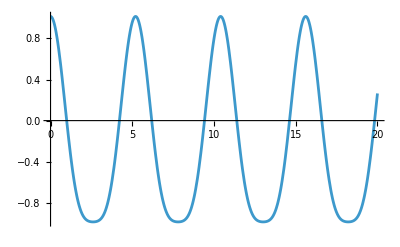

```mathematica
Plot[solu,{x,0,20}]
```

### O(ϵ^3): (u_3, v_3)

The O(ϵ^3) system is
∂/(∂t_0)(u_3
v_3) + ∂/(∂t_1)(u_2
v_2)+∂/(∂t_2)(u_1
v_1)=(d_c | 0
0 | 1)(u_3
v_3)''+(1 | a
h | b)(u_3
v_3)+ (-d2 u''_1-u_1 v_1^2-c(u_2 v_1+u_1 v_2)
u_1 v_1^2+c(u_2 v_1+u_1 v_2))
or
(d_c | 0
0 | 1)(u_3
v_3)''+ (1 | a
h | b_c)(u_3
v_3)-∂/(∂t_0)(u_3
v_3)= q_3
where
q_3=- (-d2 u''_1-u_1 v_1^2-c(u_2 v_1+u_1 v_2)
u_1 v_1^2+c(u_2 v_1+u_1 v_2))+∂/(∂t_1)(u_2
v_2)+∂/(∂t_2)(u_1
v_1)
depends only on the previous solutions (u_1, v_1) and (u_2, v_2). Even more, recall that (∂A_1)/(∂t_1)=0 and since A_2=A_1^2 we have that (∂A_2)/(∂t_1)=0. Thus ∂/(∂t_1)(u_2
v_2)=0, and
q_3=-(-d2 u''_1-u_1 v_1^2-c(u_2 v_1+u_1 v_2)
u_1 v_1^2+c(u_2 v_1+u_1 v_2))+∂/(∂t_2)(u_1
v_1).

Since ∂/(∂t_0)=0, the O(ϵ^3) system can be written as
ℒ(u_3
v_3)=q_3
The solvability condition requires that
⟨(u_3^†
v_3^†), q_3⟩=0,
where (u_3^†
v_3^†) is the nullvector of ℒ^†, i.e., 
ℒ^†(u_3^†
v_3^†)=(0
0).
but ℒ^† is the same as in the O(ϵ^2) case, thus we can use the same nullvector.

```mathematica
q3 = ({{D[u1[x], t]}, {D[v1[x], t]}})  -Oe3 /. {u3[x] -> 0, u3''[x] -> 0,v3[x] -> 0,v3''[x] -> 0, d1->0}
```

{{-d2 k^2 A[t] Cos[k x]+(A[t]^3 Cos[k x]^3)/(-a+(√(a h (-b+a h)))/h)^2+(c A[t]^3 Cos[k x] (-(a c h+b c h)/(2 (b-a h) (a h-√(-a h (b-a h))))+((-b+2 a h-2 √(a h (-b+a h))) (a c h+b c h-4 c h k^2) Cos[2 k x])/(2 (-a h+√(a h (-b+a h))) (-b^2+3 a b h-2 a^2 h^2-2 b √(a h (-b+a h))+2 a h √(a h (-b+a h))+8 b k^2-8 a h k^2+8 √(a h (-b+a h)) k^2-16 k^4))))/(-a+(√(a h (-b+a h)))/h)+c A[t]^3 Cos[k x] ((c h+c h^2)/(2 (-b+a h) (-a h+√(a h (-b+a h))))-((-b c h+2 a c h^2-b c h^2+2 a c h^3-2 c h √(a h (-b+a h))-2 c h^2 √(a h (-b+a h))+4 c h k^2) Cos[2 k x])/(2 (-a h+√(a h (-b+a h))) (-b^2+3 a b h-2 a^2 h^2-2 b √(a h (-b+a h))+2 a h √(a h (-b+a h))+8 b k^2-8 a h k^2+8 √(a h (-b+a h)) k^2-16 k^4)))+Cos[k x] A'[t]},{-(A[t]^3 Cos[k x]^3)/(-a+(√(a h (-b+a h)))/h)^2-(c A[t]^3 Cos[k x] (-(a c h+b c h)/(2 (b-a h) (a h-√(-a h (b-a h))))+((-b+2 a h-2 √(a h (-b+a h))) (a c h+b c h-4 c h k^2) Cos[2 k x])/(2 (-a h+√(a h (-b+a h))) (-b^2+3 a b h-2 a^2 h^2-2 b √(a h (-b+a h))+2 a h √(a h (-b+a h))+8 b k^2-8 a h k^2+8 √(a h (-b+a h)) k^2-16 k^4))))/(-a+(√(a h (-b+a h)))/h)-c A[t]^3 Cos[k x] ((c h+c h^2)/(2 (-b+a h) (-a h+√(a h (-b+a h))))-((-b c h+2 a c h^2-b c h^2+2 a c h^3-2 c h √(a h (-b+a h))-2 c h^2 √(a h (-b+a h))+4 c h k^2) Cos[2 k x])/(2 (-a h+√(a h (-b+a h))) (-b^2+3 a b h-2 a^2 h^2-2 b √(a h (-b+a h))+2 a h √(a h (-b+a h))+8 b k^2-8 a h k^2+8 √(a h (-b+a h)) k^2-16 k^4)))+(Cos[k x] A'[t])/(-a+(√(a h (-b+a h)))/h)}}

Since the operator ℒ^† is the same as in the previous approximations, we already found its null space is generated by:

```mathematica
{W1,W2}Cos[k x]
```

{Cos[k x],-((a h+√(a h (-b+a h))) Cos[k x])/(b h)}

The solvability condition is :

```mathematica
solva=Refine[L2IP[{W1,W2}Cos[k x],q3, {k ∈ Reals,b ∈ Reals,c ∈ Reals, d2 ∈ Reals}], Assumptions->{n∈Integers}];
```

```mathematica
solva = solva /. k-> kc
```

{(16 a b^7 d2 (b-a h+√(a h (-b+a h))) n π A[t]-48 a^2 b^6 d2 h (b-a h+√(a h (-b+a h))) n π A[t]+48 a^3 b^5 d2 h^2 (b-a h+√(a h (-b+a h))) n π A[t]-16 a^4 b^4 d2 h^3 (b-a h+√(a h (-b+a h))) n π A[t]-256 a b^6 d2 (b-a h+√(a h (-b+a h)))^2 n π A[t]+768 a^2 b^5 d2 h (b-a h+√(a h (-b+a h)))^2 n π A[t]-768 a^3 b^4 d2 h^2 (b-a h+√(a h (-b+a h)))^2 n π A[t]+256 a^4 b^3 d2 h^3 (b-a h+√(a h (-b+a h)))^2 n π A[t]+1536 a b^5 d2 (b-a h+√(a h (-b+a h)))^3 n π A[t]-4096 a^2 b^4 d2 h (b-a h+√(a h (-b+a h)))^3 n π A[t]+3584 a^3 b^3 d2 h^2 (b-a h+√(a h (-b+a h)))^3 n π A[t]-1024 a^4 b^2 d2 h^3 (b-a h+√(a h (-b+a h)))^3 n π A[t]-4096 a b^4 d2 (b-a h+√(a h (-b+a h)))^4 n π A[t]+8192 a^2 b^3 d2 h (b-a h+√(a h (-b+a h)))^4 n π A[t]-4096 a^3 b^2 d2 h^2 (b-a h+√(a h (-b+a h)))^4 n π A[t]+4096 a b^3 d2 (b-a h+√(a h (-b+a h)))^5 n π A[t]-4096 a^2 b^2 d2 h (b-a h+√(a h (-b+a h)))^5 n π A[t]+12 b^6 h n π A[t]^3+12 b^6 c^2 h n π A[t]^3-60 a b^5 h^2 n π A[t]^3-24 a^2 b^4 c^2 h^2 n π A[t]^3-60 a b^5 c^2 h^2 n π A[t]^3+108 a^2 b^4 h^3 n π A[t]^3+48 a^3 b^3 c^2 h^3 n π A[t]^3+84 a^2 b^4 c^2 h^3 n π A[t]^3-84 a^3 b^3 h^4 n π A[t]^3-24 a^4 b^2 c^2 h^4 n π A[t]^3-36 a^3 b^3 c^2 h^4 n π A[t]^3+24 a^4 b^2 h^5 n π A[t]^3-12 b^5 c^2 √(a h (-b+a h)) n π A[t]^3-24 b^5 h √(a h (-b+a h)) n π A[t]^3-36 b^5 c^2 h √(a h (-b+a h)) n π A[t]^3+72 a b^4 h^2 √(a h (-b+a h)) n π A[t]^3+36 a^2 b^3 c^2 h^2 √(a h (-b+a h)) n π A[t]^3+72 a b^4 c^2 h^2 √(a h (-b+a h)) n π A[t]^3-72 a^2 b^3 h^3 √(a h (-b+a h)) n π A[t]^3-24 a^3 b^2 c^2 h^3 √(a h (-b+a h)) n π A[t]^3-36 a^2 b^3 c^2 h^3 √(a h (-b+a h)) n π A[t]^3+24 a^3 b^2 h^4 √(a h (-b+a h)) n π A[t]^3-192 b^5 h (b-a h+√(a h (-b+a h))) n π A[t]^3+16 a b^4 c^2 h (b-a h+√(a h (-b+a h))) n π A[t]^3-176 b^5 c^2 h (b-a h+√(a h (-b+a h))) n π A[t]^3+960 a b^4 h^2 (b-a h+√(a h (-b+a h))) n π A[t]^3+160 a^2 b^3 c^2 h^2 (b-a h+√(a h (-b+a h))) n π A[t]^3+768 a b^4 c^2 h^2 (b-a h+√(a h (-b+a h))) n π A[t]^3-1728 a^2 b^3 h^3 (b-a h+√(a h (-b+a h))) n π A[t]^3-368 a^3 b^2 c^2 h^3 (b-a h+√(a h (-b+a h))) n π A[t]^3-1008 a^2 b^3 c^2 h^3 (b-a h+√(a h (-b+a h))) n π A[t]^3+1344 a^3 b^2 h^4 (b-a h+√(a h (-b+a h))) n π A[t]^3+192 a^4 b c^2 h^4 (b-a h+√(a h (-b+a h))) n π A[t]^3+416 a^3 b^2 c^2 h^4 (b-a h+√(a h (-b+a h))) n π A[t]^3-384 a^4 b h^5 (b-a h+√(a h (-b+a h))) n π A[t]^3+176 b^4 c^2 √(a h (-b+a h)) (b-a h+√(a h (-b+a h))) n π A[t]^3+384 b^4 h √(a h (-b+a h)) (b-a h+√(a h (-b+a h))) n π A[t]^3-96 a b^3 c^2 h √(a h (-b+a h)) (b-a h+√(a h (-b+a h))) n π A[t]^3+480 b^4 c^2 h √(a h (-b+a h)) (b-a h+√(a h (-b+a h))) n π A[t]^3-1152 a b^3 h^2 √(a h (-b+a h)) (b-a h+√(a h (-b+a h))) n π A[t]^3-272 a^2 b^2 c^2 h^2 √(a h (-b+a h)) (b-a h+√(a h (-b+a h))) n π A[t]^3-896 a b^3 c^2 h^2 √(a h (-b+a h)) (b-a h+√(a h (-b+a h))) n π A[t]^3+1152 a^2 b^2 h^3 √(a h (-b+a h)) (b-a h+√(a h (-b+a h))) n π A[t]^3+192 a^3 b c^2 h^3 √(a h (-b+a h)) (b-a h+√(a h (-b+a h))) n π A[t]^3+416 a^2 b^2 c^2 h^3 √(a h (-b+a h)) (b-a h+√(a h (-b+a h))) n π A[t]^3-384 a^3 b h^4 √(a h (-b+a h)) (b-a h+√(a h (-b+a h))) n π A[t]^3+1152 b^4 h (b-a h+√(a h (-b+a h)))^2 n π A[t]^3-128 a b^3 c^2 h (b-a h+√(a h (-b+a h)))^2 n π A[t]^3+960 b^4 c^2 h (b-a h+√(a h (-b+a h)))^2 n π A[t]^3-5376 a b^3 h^2 (b-a h+√(a h (-b+a h)))^2 n π A[t]^3-1152 a^2 b^2 c^2 h^2 (b-a h+√(a h (-b+a h)))^2 n π A[t]^3-3840 a b^3 c^2 h^2 (b-a h+√(a h (-b+a h)))^2 n π A[t]^3+8832 a^2 b^2 h^3 (b-a h+√(a h (-b+a h)))^2 n π A[t]^3+2304 a^3 b c^2 h^3 (b-a h+√(a h (-b+a h)))^2 n π A[t]^3+4416 a^2 b^2 c^2 h^3 (b-a h+√(a h (-b+a h)))^2 n π A[t]^3-6144 a^3 b h^4 (b-a h+√(a h (-b+a h)))^2 n π A[t]^3-1024 a^4 c^2 h^4 (b-a h+√(a h (-b+a h)))^2 n π A[t]^3-1536 a^3 b c^2 h^4 (b-a h+√(a h (-b+a h)))^2 n π A[t]^3+1536 a^4 h^5 (b-a h+√(a h (-b+a h)))^2 n π A[t]^3-960 b^3 c^2 √(a h (-b+a h)) (b-a h+√(a h (-b+a h)))^2 n π A[t]^3-2304 b^3 h √(a h (-b+a h)) (b-a h+√(a h (-b+a h)))^2 n π A[t]^3+192 a b^2 c^2 h √(a h (-b+a h)) (b-a h+√(a h (-b+a h)))^2 n π A[t]^3-2496 b^3 c^2 h √(a h (-b+a h)) (b-a h+√(a h (-b+a h)))^2 n π A[t]^3+6144 a b^2 h^2 √(a h (-b+a h)) (b-a h+√(a h (-b+a h)))^2 n π A[t]^3+1792 a^2 b c^2 h^2 √(a h (-b+a h)) (b-a h+√(a h (-b+a h)))^2 n π A[t]^3+4032 a b^2 c^2 h^2 √(a h (-b+a h)) (b-a h+√(a h (-b+a h)))^2 n π A[t]^3-5376 a^2 b h^3 √(a h (-b+a h)) (b-a h+√(a h (-b+a h)))^2 n π A[t]^3-1024 a^3 c^2 h^3 √(a h (-b+a h)) (b-a h+√(a h (-b+a h)))^2 n π A[t]^3-1536 a^2 b c^2 h^3 √(a h (-b+a h)) (b-a h+√(a h (-b+a h)))^2 n π A[t]^3+1536 a^3 h^4 √(a h (-b+a h)) (b-a h+√(a h (-b+a h)))^2 n π A[t]^3-3072 b^3 h (b-a h+√(a h (-b+a h)))^3 n π A[t]^3+256 a b^2 c^2 h (b-a h+√(a h (-b+a h)))^3 n π A[t]^3-2304 b^3 c^2 h (b-a h+√(a h (-b+a h)))^3 n π A[t]^3+12288 a b^2 h^2 (b-a h+√(a h (-b+a h)))^3 n π A[t]^3+3840 a^2 b c^2 h^2 (b-a h+√(a h (-b+a h)))^3 n π A[t]^3+8448 a b^2 c^2 h^2 (b-a h+√(a h (-b+a h)))^3 n π A[t]^3-15360 a^2 b h^3 (b-a h+√(a h (-b+a h)))^3 n π A[t]^3-4096 a^3 c^2 h^3 (b-a h+√(a h (-b+a h)))^3 n π A[t]^3-6144 a^2 b c^2 h^3 (b-a h+√(a h (-b+a h)))^3 n π A[t]^3+6144 a^3 h^4 (b-a h+√(a h (-b+a h)))^3 n π A[t]^3+2304 b^2 c^2 √(a h (-b+a h)) (b-a h+√(a h (-b+a h)))^3 n π A[t]^3+6144 b^2 h √(a h (-b+a h)) (b-a h+√(a h (-b+a h)))^3 n π A[t]^3+1792 a b c^2 h √(a h (-b+a h)) (b-a h+√(a h (-b+a h)))^3 n π A[t]^3+6144 b^2 c^2 h √(a h (-b+a h)) (b-a h+√(a h (-b+a h)))^3 n π A[t]^3-12288 a b h^2 √(a h (-b+a h)) (b-a h+√(a h (-b+a h)))^3 n π A[t]^3-4096 a^2 c^2 h^2 √(a h (-b+a h)) (b-a h+√(a h (-b+a h)))^3 n π A[t]^3-6144 a b c^2 h^2 √(a h (-b+a h)) (b-a h+√(a h (-b+a h)))^3 n π A[t]^3+6144 a^2 h^3 √(a h (-b+a h)) (b-a h+√(a h (-b+a h)))^3 n π A[t]^3+3072 b^2 h (b-a h+√(a h (-b+a h)))^4 n π A[t]^3+2048 b^2 c^2 h (b-a h+√(a h (-b+a h)))^4 n π A[t]^3-9216 a b h^2 (b-a h+√(a h (-b+a h)))^4 n π A[t]^3-4096 a^2 c^2 h^2 (b-a h+√(a h (-b+a h)))^4 n π A[t]^3-6144 a b c^2 h^2 (b-a h+√(a h (-b+a h)))^4 n π A[t]^3+6144 a^2 h^3 (b-a h+√(a h (-b+a h)))^4 n π A[t]^3-2048 b c^2 √(a h (-b+a h)) (b-a h+√(a h (-b+a h)))^4 n π A[t]^3-6144 b h √(a h (-b+a h)) (b-a h+√(a h (-b+a h)))^4 n π A[t]^3-4096 a c^2 h √(a h (-b+a h)) (b-a h+√(a h (-b+a h)))^4 n π A[t]^3-6144 b c^2 h √(a h (-b+a h)) (b-a h+√(a h (-b+a h)))^4 n π A[t]^3+6144 a h^2 √(a h (-b+a h)) (b-a h+√(a h (-b+a h)))^4 n π A[t]^3-16 a b^7 n π A'[t]+48 a^2 b^6 h n π A'[t]-48 a^3 b^5 h^2 n π A'[t]+16 a^4 b^4 h^3 n π A'[t]+256 a b^6 (b-a h+√(a h (-b+a h))) n π A'[t]-768 a^2 b^5 h (b-a h+√(a h (-b+a h))) n π A'[t]+768 a^3 b^4 h^2 (b-a h+√(a h (-b+a h))) n π A'[t]-256 a^4 b^3 h^3 (b-a h+√(a h (-b+a h))) n π A'[t]-1536 a b^5 (b-a h+√(a h (-b+a h)))^2 n π A'[t]+4096 a^2 b^4 h (b-a h+√(a h (-b+a h)))^2 n π A'[t]-3584 a^3 b^3 h^2 (b-a h+√(a h (-b+a h)))^2 n π A'[t]+1024 a^4 b^2 h^3 (b-a h+√(a h (-b+a h)))^2 n π A'[t]+4096 a b^4 (b-a h+√(a h (-b+a h)))^3 n π A'[t]-8192 a^2 b^3 h (b-a h+√(a h (-b+a h)))^3 n π A'[t]+4096 a^3 b^2 h^2 (b-a h+√(a h (-b+a h)))^3 n π A'[t]-4096 a b^3 (b-a h+√(a h (-b+a h)))^4 n π A'[t]+4096 a^2 b^2 h (b-a h+√(a h (-b+a h)))^4 n π A'[t])/(32 a b^2 (-b+a h) √(b-a h+√(a h (-b+a h))) (b^2-a b h-8 b (b-a h+√(a h (-b+a h)))+8 a h (b-a h+√(a h (-b+a h)))+16 (b-a h+√(a h (-b+a h)))^2)^2)-1/(32 a b^3 h (-b+a h) √(b-a h+√(a h (-b+a h))))(a h+√(a h (-b+a h))) (-((4 (3 b^6 (1+c^2) h+128 a h (-2 c^2+3 h) (b-a h+√(a h (-b+a h)))^2 (a h+√(a h (-b+a h))) (a h+2 (b-a h+√(a h (-b+a h))))^2-b^5 (15 a (1+c^2) h^2+6 h (√(a h (-b+a h))+8 (b-a h+√(a h (-b+a h))))+c^2 (3 √(a h (-b+a h))+9 h √(a h (-b+a h))+44 h (b-a h+√(a h (-b+a h)))))+2 b^2 (3 a^4 h^4 (-c^2+h)+a^3 h^3 (3 h (√(a h (-b+a h))+56 (b-a h+√(a h (-b+a h))))-c^2 (3 √(a h (-b+a h))+(46-52 h) (b-a h+√(a h (-b+a h)))))+8 a h (b-a h+√(a h (-b+a h)))^2 (96 h (√(a h (-b+a h))+2 (b-a h+√(a h (-b+a h))))+c^2 (3 √(a h (-b+a h))+63 h √(a h (-b+a h))+4 (b-a h+√(a h (-b+a h)))+132 h (b-a h+√(a h (-b+a h)))))+2 a^2 h^2 (b-a h+√(a h (-b+a h))) (72 h √(a h (-b+a h))+552 h (b-a h+√(a h (-b+a h)))+c^2 (-17 √(a h (-b+a h))+26 h √(a h (-b+a h))-72 (b-a h+√(a h (-b+a h)))+276 h (b-a h+√(a h (-b+a h)))))+32 (b-a h+√(a h (-b+a h)))^3 (12 h (b-a h+3 √(a h (-b+a h)))+c^2 (9 √(a h (-b+a h))+8 h (b-a h+4 √(a h (-b+a h))))))-16 b (b-a h+√(a h (-b+a h))) (a h+2 (b-a h+√(a h (-b+a h)))) (-3 a^3 (c^2-2 h) h^3+16 √(a h (-b+a h)) (3 h+c^2 (1+3 h)) (b-a h+√(a h (-b+a h)))^2+3 a^2 h^2 (2 h (√(a h (-b+a h))+14 (b-a h+√(a h (-b+a h))))-c^2 (√(a h (-b+a h))+(10-8 h) (b-a h+√(a h (-b+a h)))))+2 a h (b-a h+√(a h (-b+a h))) (36 h (b-a h+2 √(a h (-b+a h)))+c^2 (-11 √(a h (-b+a h))+12 h (√(a h (-b+a h))+2 (b-a h+√(a h (-b+a h)))))))-b^3 (3 a^3 h^3 (7 h+c^2 (-4+3 h))+48 (b-a h+√(a h (-b+a h)))^2 (4 h (3 √(a h (-b+a h))+4 (b-a h+√(a h (-b+a h))))+c^2 (5 √(a h (-b+a h))+13 h √(a h (-b+a h))+12 h (b-a h+√(a h (-b+a h)))))+8 a h (b-a h+√(a h (-b+a h))) (36 h √(a h (-b+a h))+168 h (b-a h+√(a h (-b+a h)))+c^2 (3 √(a h (-b+a h))+28 h √(a h (-b+a h))+4 (b-a h+√(a h (-b+a h)))+120 h (b-a h+√(a h (-b+a h)))))+a^2 h^2 (18 h (√(a h (-b+a h))+24 (b-a h+√(a h (-b+a h))))+c^2 (-9 √(a h (-b+a h))-40 (b-a h+√(a h (-b+a h)))+9 h (√(a h (-b+a h))+28 (b-a h+√(a h (-b+a h)))))))+b^4 (3 a^2 h^2 (9 h+c^2 (-2+7 h))+4 (b-a h+√(a h (-b+a h))) (24 h (√(a h (-b+a h))+3 (b-a h+√(a h (-b+a h))))+c^2 (11 √(a h (-b+a h))+30 h (√(a h (-b+a h))+2 (b-a h+√(a h (-b+a h))))))+2 a h (2 c^2 (b-a h+√(a h (-b+a h)))+3 h (3 √(a h (-b+a h))+40 (b-a h+√(a h (-b+a h)))+c^2 (3 √(a h (-b+a h))+32 (b-a h+√(a h (-b+a h)))))))) n π A[t]^3)/(b^2-a b h-8 b (b-a h+√(a h (-b+a h)))+8 a h (b-a h+√(a h (-b+a h)))+16 (b-a h+√(a h (-b+a h)))^2)^2)+16 b (b-a h) (a h+√(a h (-b+a h))) n π A'[t])}

```mathematica
sol = Solve[ solva== 0, A'[t]]
```

```mathematica
rhs = A'[t] /.sol [[1]] // Expand
```

```mathematica
coefA = Coefficient[rhs, A[t]] //Simplify
```

(d2 (b-a h+√(a h (-b+a h))) (-9 b^2+128 a h (-a h+√(a h (-b+a h)))-16 b (-7 a h+3 √(a h (-b+a h)))))/(-9 b^2-128 a^2 h^2+30 √(a h (-b+a h))+b (9+112 a h-48 √(a h (-b+a h)))+2 a h (-17+64 √(a h (-b+a h))))

```mathematica
coefA3 = Coefficient[rhs, A[t]^3] // Simplify
```

(4 a^3 (23 c^2-27 h) h^2-27 b^2 (b (9+5 c^2) h+3 √(a h (-b+a h)) (3+10 h+3 c^2 h))+a^2 h (-459 b h (1+2 h)-4 (-23 c^2+27 h) √(a h (-b+a h))+b c^2 (993+2584 h+1472 h^2))-a b (9 b (-3 h (21+43 h)+c^2 (15+76 h+43 h^2))+√(a h (-b+a h)) (-27 h (13+30 h)+c^2 (657+2280 h+1472 h^2))))/(36 a b (-b+a h) (9 b^2+128 a^2 h^2-30 √(a h (-b+a h))+b (-9-112 a h+48 √(a h (-b+a h)))-2 a h (-17+64 √(a h (-b+a h)))))

The Stuart-Landau equation is then:
          coefAp(∂A)/(∂t_2)=coefA A[t] - coefA3 A[t]^3 
or
         (∂A)/(∂t_2)= α A[t]- β A[t]^3 
where:
  α=coefA , and  β= -coefA3

The SL equation can be written also as (see Notes)

(∂A)/(∂t)= (d_c-d)α' A[t]- β A[t]^3 

where

α'=α/d_2.

```mathematica
α = FullSimplify[coefA ]
```

(d2 (b^3+5 a b h-3 b √(a h (-b+a h))+b^2 (-1-a h+√(a h (-b+a h)))+4 a h (-a h+√(a h (-b+a h)))))/((-1+b)^2+4 a h)

```mathematica
αp = α/d2
```

(b^3+5 a b h-3 b √(a h (-b+a h))+b^2 (-1-a h+√(a h (-b+a h)))+4 a h (-a h+√(a h (-b+a h))))/((-1+b)^2+4 a h)

```mathematica
β= FullSimplify[-coefA3]
```

(4 a^3 h^2 (-23 c^2+27 h)+27 b^2 (b (9+5 c^2) h+3 √(a h (-b+a h)) (3+10 h+3 c^2 h))+a^2 h (459 b h (1+2 h)+4 (-23 c^2+27 h) √(a h (-b+a h))-b c^2 (993+8 h (323+184 h)))+a b (9 b (-3 h (21+43 h)+c^2 (15+h (76+43 h)))+√(a h (-b+a h)) (-27 h (13+30 h)+c^2 (657+8 h (285+184 h)))))/(36 a b (-b+a h) (9 b^2-30 √(a h (-b+a h))+2 a h (17+64 a h-64 √(a h (-b+a h)))+b (-9-112 a h+48 √(a h (-b+a h)))))

The solution of the Stuart-Landau equation:

(∂A)/(∂t)= (d_c-d)α' A[t]-β A[t]^3 

 is (see notes, pag. 24):

A^2= 1/(β/((d_c-d)α')+k ⅇ^(-2(d_c-d)α' t)),      k∈R
or
A^2= 1/(β/((d_c-d)α')+k ⅇ^(-2(d_c-d)α' t))
Since

```mathematica
Amplitude = √(((dc-d)αp)/β)  // FullSimplify
```

6 √((a b (-b+a h) (b^3+5 a b h-3 b √(a h (-b+a h))+b^2 (-1-a h+√(a h (-b+a h)))+4 a h (-a h+√(a h (-b+a h)))) (-d+1/(b-2 a h+2 √(a h (-b+a h)))) (9 b^2-30 √(a h (-b+a h))+2 a h (17+64 a h-64 √(a h (-b+a h)))+b (-9-112 a h+48 √(a h (-b+a h)))))/(((-1+b)^2+4 a h) (4 a^3 h^2 (-23 c^2+27 h)+27 b^2 (b (9+5 c^2) h+3 √(a h (-b+a h)) (3+10 h+3 c^2 h))+a^2 h (459 b h (1+2 h)+4 (-23 c^2+27 h) √(a h (-b+a h))-b c^2 (993+8 h (323+184 h)))+a b (9 b (-3 h (21+43 h)+c^2 (15+h (76+43 h)))+√(a h (-b+a h)) (-27 h (13+30 h)+c^2 (657+8 h (285+184 h)))))))

```mathematica
Refine[Amplitude, Assumptions->{a>0, b<0, h>0, c∈Reals}]
```

6 √(-1/((-1+b)^2+4 a h)a b (-b+a h) (-b^3-5 a b h+3 b √(a h (-b+a h))-b^2 (-1-a h+√(a h (-b+a h)))-4 a h (-a h+√(a h (-b+a h)))) (9 b^2-30 √(a h (-b+a h))+2 a h (17+64 a h-64 √(a h (-b+a h)))+b (-9-112 a h+48 √(a h (-b+a h))))) √((-d+1/(b-2 a h+2 √(a h (-b+a h))))/(4 a^3 h^2 (-23 c^2+27 h)+27 b^2 (b (9+5 c^2) h+3 √(a h (-b+a h)) (3+10 h+3 c^2 h))+a^2 h (459 b h (1+2 h)+4 (-23 c^2+27 h) √(a h (-b+a h))-b c^2 (993+8 h (323+184 h)))+a b (9 b (-3 h (21+43 h)+c^2 (15+h (76+43 h)))+√(a h (-b+a h)) (-27 h (13+30 h)+c^2 (657+8 h (285+184 h))))))